```mathematica
(* This Notebook defines modules to find ϕ[n], ϵ[n], η[n],ns[n], Zϵ, and Zη. It does not use the slow roll approx and instead integrates the Klein Gordon equation to find ϕ[n]. It then plots where monomial potentials fall on the r-ns plane and prints out the degrees of fine tuning. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
(* v[x_] := x^4*(1-Log[x]) *)
v[x_] := x^4
vp[x_]=v'[x]
```

4 x^3

{{ϕ→InterpolatingFunction[{{0., 70.}}, <>]}}

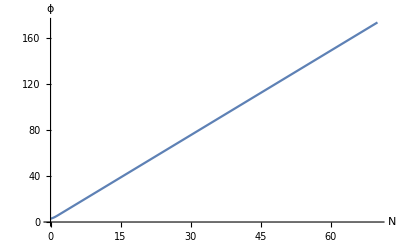

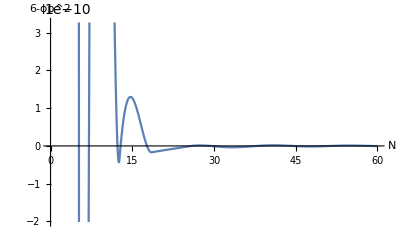

```mathematica
(* Define a module to find ϕ[n] integrating from ϕ0 instead of ϕ60 *)
findϕUsingϕ0 := Module[{h,hsq,nsr,ϕ0,ϕp0},
(* Define H as a function of number of efolds 
Input: v[ϕ[n]], vp[ϕ[n]]
Output: ϕsol[n] *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
(* find ϕp0 = ϕ'[0] *)
ϕp0 = vp[ϕ0]/v[ϕ0] ;
(* Solve for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[0]==ϕ0,ϕ'[0]==ϕp0},ϕ,{n,0,70},InterpolationOrder->All]]
ϕsol = findϕUsingϕ0
Plot[Evaluate[ϕ[n]/.ϕsol],{n,70,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

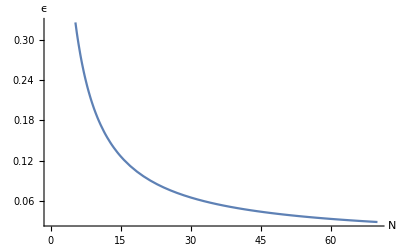

{1.}

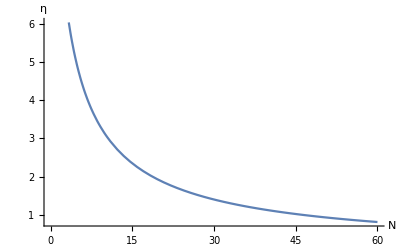

```mathematica
(* Find the slow-roll parameters ϵ[n] and η[n] *)
findϵ := Module[{ϵ},
(* Find ϵ[n] 
Input: v[ϕ[n]], ϕsol 
Output: ϵ[n] *)
ϵ[n_] := 1/2*D[Log[v[ϕ[n]/.ϕsol]],n];
Return[ϵ[n]]]
ϵ[n_] := findϵ 
Plot[Evaluate[ϵ[n]],{n,70,0},AxesLabel->{N,ϵ}]
ϵ[n]/.{n->0}

findη := Module[{ϕp,η},
(* Find η[n] 
Input: v[x], vp[ϕ[n]], ϕsol
Output: η[n] *)
ϕp[x_] := v'[x]/v[x];
η[n_] := 1/2*D[Log[vp[ϕ[n]/.ϕsol]]^2,n];
Return[η[n]]]
η[n_] := findη
Plot[Evaluate[η[n]],{n,60,0},AxesLabel->{N,η}]
```

ns[60] = {0.917764}

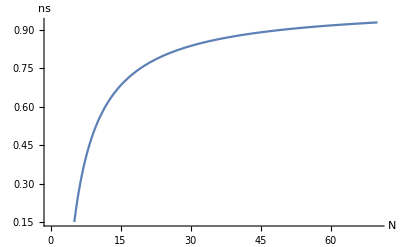

```mathematica
(* Find the spectral tilt: ns[n] *)
findNs := Module[{ns,ϕ60},
(* Find ns[n]
Input: ϵ[n],
Output: ns[n] *)
ns[n_] := 1-2*ϵ[n]+D[Log[ϵ[n]],n];
Return[ns[n]]]
ns[n_] := findNs
Print["ns[60] = ",ns[n]/.{n->60}]
Plot[Evaluate[ns[n]],{n,70,0},AxesLabel->{N,ns}]
```

```mathematica
(* Find the degrees of fine-tuning: Zϵ and Zη *)
findZϵ := Module[{roots},
(* Find Zϵ 
Input: ϵ[n], 
Output: Zϵ *)
roots = Solve[ϵ[n]==0,n,{n,0,60}];
roots = Normal[Select[Association[roots],#>0&#<60&]];
Print["Roots = ",roots];
Return[Length[roots]]]
Zϵ = findZϵ

findZη := Module[{roots},
(* Find Zη
Input: η[n], 
Output: Zη *)
roots = Solve[η[n]==0,n,{n,0,60}];
roots = Normal[Select[Association[roots],#>0&#<60&]];
Print["Roots = ",roots];
Return[Length[roots]]]
Zη = findZη
```

Solve::ivar: 0 is not a valid variable.

Roots = {}

0

Solve::ivar: 0 is not a valid variable.

Roots = {}

0